```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mTsq,s12,s16,s345};
For[i=1,i<=4,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=3;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

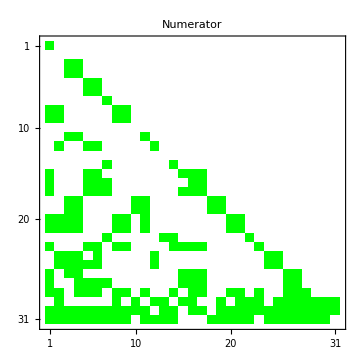
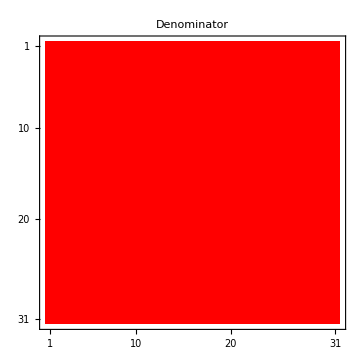
-Graphics- | -Graphics- |

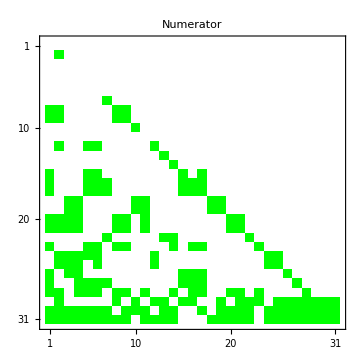
-Graphics- | -Graphics- |

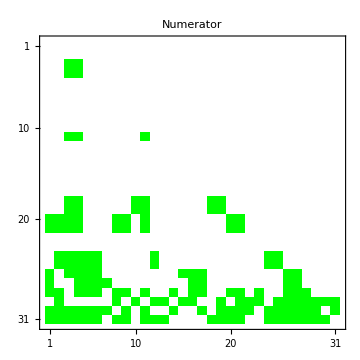
-Graphics- | -Graphics- |

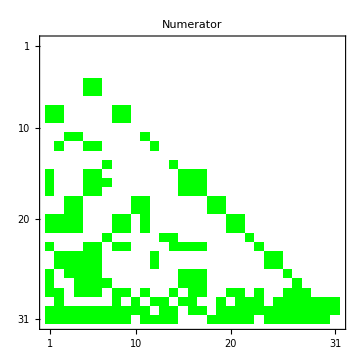
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=31;
For[i=1,i<=4,i++,
MatReco[diffInvariants[[i]]]=Table[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P],{pos,1,Length[dhxbMatrices[s12][[1]]]}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{31,31}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{31,31}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
Expand[ArrayReshape[MatReco[diffInvariants[[1]]],{31,31}],Modulus->31]//MatrixForm
```

(12 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 ϵ | 16 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7 ϵ | 13 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 17 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 13 ϵ | 10 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 22 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23 ϵ | 15 ϵ | 0 | 0 | 0 | 0 | 0 | 25 ϵ | 8 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30 ϵ | 26 ϵ | 0 | 0 | 0 | 0 | 0 | 6 ϵ | 20 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ϵ | 15 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 14 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15 ϵ | 0 | 0 | 9 ϵ | 9 ϵ | 0 | 0 | 0 | 0 | 0 | 14 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 17 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 10 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 ϵ | 0 | 0 | 0 | 9 ϵ | 5 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ϵ | 21 ϵ | 26 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29 ϵ | 0 | 0 | 0 | 17 ϵ | 13 ϵ | 17 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 ϵ | 8 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 ϵ | 0 | 0 | 0 | 21 ϵ | 21 ϵ | 21 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27 ϵ | 11 ϵ | 11 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 15 ϵ | 12 ϵ | 0 | 0 | 0 | 0 | 0 | 18 ϵ | 22 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 27 ϵ | 7 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 22 ϵ | 5 ϵ | 0 | 0 | 0 | 0 | 0 | 17 ϵ | 20 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 12 ϵ | 15 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 ϵ | 4 ϵ | 4 ϵ | 21 ϵ | 0 | 0 | 0 | 6 ϵ | 29 ϵ | 0 | 30 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 ϵ | 5 ϵ | 17 ϵ | 13 ϵ | 0 | 0 | 0 | 9 ϵ | 7 ϵ | 0 | 14 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 ϵ | 9 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 17 ϵ | 0 | 0 | 0 | 0 | 0 | 15 ϵ | 24 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25 ϵ | 0 | 0 | 0 | 23 ϵ | 27 ϵ | 0 | 27 ϵ | 9 ϵ | 0 | 0 | 0 | 0 | 23 ϵ | 5 ϵ | 5 ϵ | 23 ϵ | 0 | 0 | 0 | 0 | 0 | 2 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16 ϵ | 0 | 24 ϵ | 0 | 24 ϵ | 0 | 0 | 0 | 0 | 0 | 10 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 ϵ | 16 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 29 ϵ | 2 ϵ | 29 ϵ | 10 ϵ | 12 ϵ | 0 | 0 | 0 | 0 | 0 | 9 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 ϵ | 15 ϵ | 0 | 0 | 0 | 0 | 0 | 0
21 ϵ | 0 | 4 ϵ | 25 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 ϵ | 11 ϵ | 2 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 ϵ | 16 ϵ | 0 | 0 | 0 | 0
27 ϵ | 0 | 0 | 21 ϵ | 11 ϵ | 28 ϵ | 2 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 ϵ | 16 ϵ | 2 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 ϵ | 30 ϵ | 0 | 0 | 0 | 0
27 ϵ | 11 ϵ | 0 | ϵ | 12 ϵ | 11 ϵ | 0 | 26 ϵ | 20 ϵ | 0 | 2 ϵ | 0 | 0 | 12 ϵ | 0 | 3 ϵ | 12 ϵ | 0 | 0 | 30 ϵ | 20 ϵ | 0 | 26 ϵ | 0 | 0 | 2 ϵ | 2 ϵ | 21 ϵ | 0 | 0 | 0
0 | 27 ϵ | 0 | 0 | 0 | 0 | 0 | 14 ϵ | 0 | 29 ϵ | 0 | 20 ϵ | 30 ϵ | 0 | 25 ϵ | 12 ϵ | 0 | 0 | 16 ϵ | 0 | 10 ϵ | 14 ϵ | 14 ϵ | 0 | 8 ϵ | 22 ϵ | 22 ϵ | 24 ϵ | 16 ϵ | 14 ϵ | 30 ϵ
18 ϵ | 0 | 10 ϵ | 23 ϵ | 22 ϵ | 21 ϵ | 10 ϵ | 22 ϵ | 20 ϵ | 7 ϵ | 18 ϵ | 0 | 15 ϵ | 12 ϵ | 0 | 21 ϵ | ϵ | 0 | 7 ϵ | 14 ϵ | 4 ϵ | 26 ϵ | 22 ϵ | 2 ϵ | 0 | 11 ϵ | 17 ϵ | 12 ϵ | 4 ϵ | 14 ϵ | 12 ϵ
20 ϵ | 17 ϵ | 30 ϵ | 30 ϵ | 21 ϵ | 13 ϵ | 6 ϵ | 6 ϵ | 25 ϵ | 0 | 27 ϵ | 6 ϵ | 30 ϵ | 20 ϵ | 0 | 0 | 0 | 11 ϵ | 8 ϵ | 11 ϵ | 12 ϵ | 17 ϵ | 0 | 29 ϵ | 28 ϵ | 28 ϵ | 28 ϵ | 12 ϵ | 24 ϵ | 28 ϵ | 0)